```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/out.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

```mathematica
arrows=Table[{Arrowheads[.01],Arrow[{
cdata[[i]],cdata[[i]]+
(vdata[[i]]/(Max[Abs[vdata]]+1.0))*3.0
}]}, {i, Length[raw]}];
```

```mathematica
Max[Abs[vdata]]
```

0.000042

```mathematica
gg=Graphics3D[arrows,Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large]
```

-Graphics3D-

```mathematica
(*ListContourPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}], PlotRange->All, PlotLegends->Automatic]*)
```

```mathematica
(*ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}],ColorFunction->"TemperatureMap",PlotLegends->Automatic, PlotRange->All]*)
```

```mathematica
(*ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}],ColorFunction->"BlueGreenYellow",PlotLegends->Automatic, PlotRange->All]*)
```

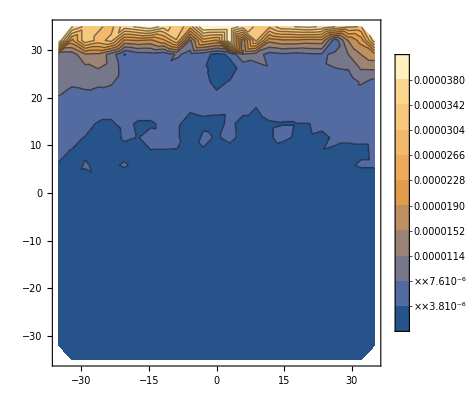

```mathematica
ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], Sqrt[raw[[All, 12]]^2+raw[[All, 13]]^2+raw[[All, 14]]^2]}], PlotRange->All, PlotLegends->Automatic, Contours->10]
```

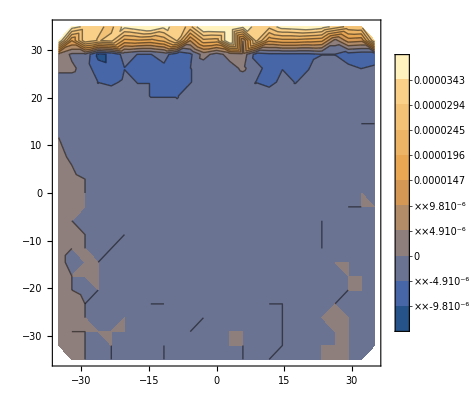

```mathematica
ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 12]]}], PlotRange->All, PlotLegends->Automatic, Contours->10]
```

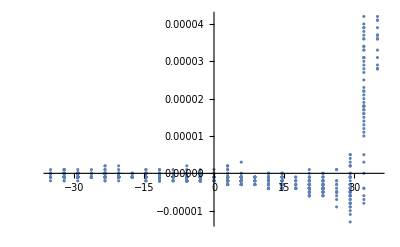

```mathematica
ListPlot[Transpose[{raw[[All, 9]], raw[[All, 12]]}], PlotRange->All]
```

```mathematica
l=Abs[Max[Flatten[cdata]]-Min[Flatten[cdata]]]
```

70.

```mathematica
sw=0.01
ew=1.0
```

0.01

1.

```mathematica
slice=Select[raw,(-sw<#[[8]]/l<sw&&#[[9]]/l+0.5<=1(*&&#[[9]]/l+0.5>ew/l*))&];
```

```mathematica
vs=Max[slice[[All, 12]]]
```

0.000022

```mathematica
ldd=Transpose[{slice[[All, 9]]/l+0.5, slice[[All, 12]]/vs}];
```

```mathematica
hues=Table[Hue[slice[[i, 10]]+1.5], {i, Length[slice]}]
```

{Hue[2.900655],Hue[0.09934500000000002],Hue[2.900655],Hue[2.900655],Hue[2.900655],Hue[0.09934500000000002],Hue[0.09934500000000002],Hue[2.900655],Hue[2.900655],Hue[0.09934500000000002],Hue[0.09934500000000002],Hue[2.900655],Hue[0.09934500000000002],Hue[0.09934500000000002],Hue[0.09934500000000002],Hue[2.900655]}

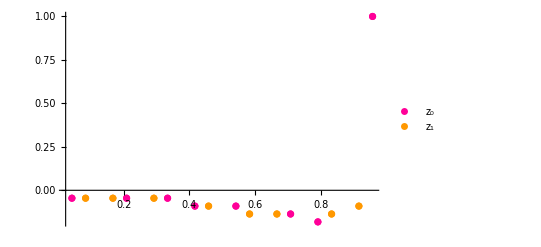

```mathematica
ldcp=ListPlot[{#}&/@ldd, PlotRange->All, PlotStyle->hues, PlotLegends->{"z_0", "z_1"}]
```

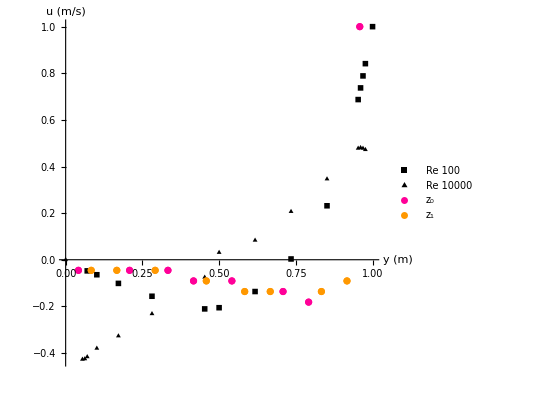

```mathematica
bpl=Show[ListPlot[{
{1, 1}, {0.9766, 0.84123}, {0.9688,0.78871}, {0.9609,0.73722}, 
{0.9531,0.68717}, {0.8516,0.23151}, {0.7344,0.00332},
 {0.6172,-0.13641}, {0.5,-0.20581},{0.4531,-0.21090}, 
{0.2813,-0.15662},{0.1719,-0.10150}, {0.1016,-0.06434}, {0.0703,-0.04775}
}, PlotStyle->Black, PlotMarkers->■, PlotLegends->{"Re 100"}],
ListPlot[{
{1, 1}, {0.9766, 0.47221}, {0.9688,0.47783}, {0.9609,0.48070}, 
{0.9531,0.47804}, {0.8516,0.34635}, {0.7344,0.20673},
 {0.6172,0.08344}, {0.5,0.03111},{0.4531,-0.07540}, 
{0.2813,-0.23186},{0.1719,-0.32709}, {0.1016,-0.38000}, {0.0703,-0.41657},
{0.0625, -0.42537}, {0.0547,-0.42735}, {0,0}
}, PlotStyle->Black, PlotMarkers->▲, PlotLegends->{"Re 10000"}],ldcp, AspectRatio->1, AxesLabel->{"y (m)", "u (m/s)"}, PlotRange->All]
```

```mathematica
Export["~/Dropbox/lidbench.pdf", bpl]
```

~/Dropbox/lidbench.pdf

```mathematica
c1=Flatten[ImportString["
92.245004
42.812085
30.084846
40.784963
54.812189
33.288674
11.760092
31.021703
35.399903
24.217382
6.343831
13.073228
18.947043
14.947577
6.469257
6.039499
11.772088
12.599574
9.333285
7.333789
5.065382
4.684782

", "Table"]];
```

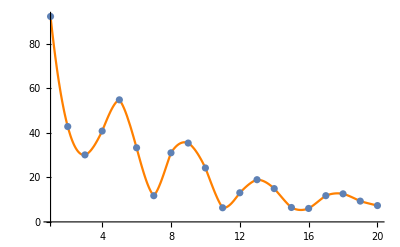

```mathematica
Show[Plot[Interpolation[c1][x], {x, 1, 20}, PlotStyle->Orange], ListPlot[c1]]
```